### A collection of procedures for analyzing recurrence equations

Here we provide some useful procedures  You need to activate these procedures (Shift-Enter) before you can use them! You also need to  define the function f. All procedures assume that f is defined as a function of two variables: N and R. Following the conventions of Mathematica, we avoid giving capital-letter symbols and replace N and R by n and r when defining functions and procedures. Hence, taking the Verhulst model (N_(t+1) = f(N_t,R) = R N_t (1-N_t)) as an example, the function f should be defined as follows:

```mathematica
Quit[]
```

```mathematica
f[n_,r_]:=r n (1-n)
```

Equilibrium analysis:  The equilibria of the model satisfy the relationship:  N^*= f[N^*,R] and are calculated as follows:

```mathematica
eq=Flatten[Values[Solve[f[n,r]==n,n]]] (* Impose the equilibrium condition *)
eq0= eq[[1]] (* Select each of the equilibria and give them a new name. You need to do this for all equilibria *)
eq1= eq[[2]]
```

{0,(-1+r)/r}

0

(-1+r)/r

Stability analysis:

```mathematica
df0 = D[f[n,r],n]/.{n->eq0}//Simplify  (* What are the derivatives of F at the equilibrium points? *)
Reduce[df0>-1&&df0<1,r]   (* For which values of R is eq0 stable? *)
Reduce[df0<0,r]                          (* For which values of R do oscillations occur around eq0? *)
```

r

-1<r<1

r<0

```mathematica
df1 = D[f[n,r],n]/.{n->eq1}//Simplify
Reduce[df1>-1&&df1<1,r]   (* For which values of R is eq1 stable? *)
Reduce[df1<0,r]                          (* For which values of R do oscillations occur around eq1? *)
```

2-r

1<r<3

r>2

Time plots:  You can show, given a model f, how n(t) changes through time.

```mathematica
tmax=10;  (*Maximum time*)
n0=0.1;(*The initial condition*)
ns=Table[0,tmax];   (*Create a table filled with 0*)
ns[[1]]=n0;
Do[ns[[t+1]]=N[f[ns[[t]],1]],{t,1,tmax-1}]  (*Recursively compute the values for the table by applying the function g*)
ListLinePlot[Table[{t,ns[[t]]},{t,1,10}],PlotStyle->Blue] (*Plot the line*)
```

It is also possible to wrap the same procedure in a function that yields the same output, using the command “Module”. This is the approach that will be adopted from now on.
The procedure timePlot[f,r,n0,tmax] makes a time plot for the model f, from t=0 to t=tmax for the given parameter value r and the given initial condition n(0)=n0. Since we want to use the procedure for various models, we have defined a general PlotRange. For specific models (like the Verhulst model), a more specific range (like PlotRange→{0.0,1.0}) may be more adequate. We therefore define two versions of the timePlot command:

```mathematica
timePlot[f_,r_,n0_,tmax_]:=Module[{pts,n},
pts=RecurrenceTable[
{n[t+1]==f[n[t],r],n[1]==n0}(* Recursively compute the values according to the model, given the initial value at time 1 *)
,n,{t,1,tmax}];ListLinePlot[pts,PlotStyle->Blue,PlotRange->All,Frame->True,FrameLabel->{Style[t,FontSize->20],Style[n,FontSize->20]}]
]
```

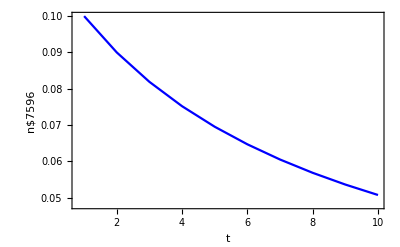

```mathematica
timePlot[f, 1, 0.1, 10]
```

```mathematica
timePlot01[f_,r_,n0_,tmax_]:=Module[{pts,n},
pts=RecurrenceTable[
{n[t+1]==f[n[t],r],n[1]==n0},(* Recursively compute the values according to the model, given the initial value at time 1 *)
n,{t,1,tmax}];
ListLinePlot[pts,PlotStyle->Blue,PlotRange->{0.0,1.0},Frame->True,FrameLabel->{Style[t,FontSize->20],Style[n,FontSize->20]}]
]
```

Dependence on initial conditions: The procedure compareSimulations[f,r,n0] illustrates potential sensitive dependence on initial conditions by comparing the fate of two populations that have almost the same initial conditions (they differ by an amount ϵ ; you may change the specified value ϵ = 0.0001 if you like).

```mathematica
compareSimulations[f_,r_,n0_]:=Module[{ϵ = 0.0001, T=30, t,nA,nB,ptsA,ptsB,ptsΔ},
(* set initial conditions *)
nA=n0;
nB=n0+ϵ;
(* simulate the recurrence equation for T time steps *)
{ptsA,ptsB,ptsΔ}=Reap[ (* collect the data generated by the Sow[] statements below *)
Do[
nA = f[nA,r];
nB = f[nB,r];
Sow[{t,nA},A]; (* store timeseries A *)
Sow[{t,nB},B]; (* store timeseries B *)
Sow[{t,nA - nB},Δ]; (* store difference *)
,{t,1,T}
]
][[2]];
GraphicsColumn[{
ListLinePlot[{ptsA,ptsB},PlotStyle->{Red,Blue},PlotRange->All,Frame->True,
FrameLabel->{Style["t",FontSize->20],Style["n_a,n_b",FontSize->20]}],
ListLinePlot[ptsΔ,PlotStyle->Red,PlotRange->All,Frame->True,
FrameLabel->{Style["t",FontSize->20],Style["n_a-n_b",FontSize->20]}]}]
]
```

Cobweb graph: The procedure cobweb[r] produces a cobweb graph for the given parameter r.

```mathematica
cobweb[f_,r_]:=Module[{n0 = 0.001, T=100, t,n1,pts},
(* simulate the recurrence equation for T time steps *)
pts=Reap[ (* collect the data generated by the Sow[] statements below *)
Do[
n1 = f[n0,r];
Sow[{n0,n0}]; (* store the points on the diagonal *)
Sow[{n0,n1}]; (* store the off-diagonal points *)
n0=n1,{t,1,T}
]
][[2]]//First;
(* draw the graph of f[N, par], plot the trajectory, and show the two graphs combined *)
Show[{Plot[{n,f[n,r]},{n,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->{{Dashed,Orange},{Thick,Orange}},AspectRatio->1,Frame->True],
ListPlot[pts,Joined->True,Mesh->All,PlotStyle->Blue,PlotRange->All]}]
]
```

Cobweb and time plot combined: The procedure cobTimePlot[r,maxN] shows a combination of a cobweb diagram and the corresponding time plot. This is particularly useful in combination with animations (with Manipulate). The parameter maxN determines the scale of the plots: N-values range from 0 to maxN.

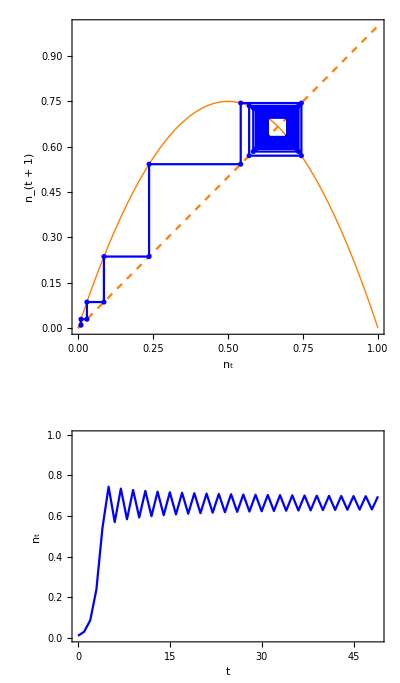

```mathematica
cobTimePlot[f_,r_,maxN_]:=Module[{n0 = 0.01, T=50, t,n1,ptsC, ptsT},
(* simulate the recurrence equation for T time steps *)
{ptsC,ptsT}=Reap[ (* collect the data generated by the Sow[] statements below *)
Do[
n1 = f[n0,r];
Sow[{n0,n0},C];      (* store the points on the diagonal of cobweb diagram *)
Sow[{n0,n1},C];      (* store the off-diagonal points of cobweb diagram *)
Sow[{t-1,n0},T];  (* store time series *)
n0=n1,
{t,1,T} ]
   ][[2]];
(* for the cobweb diagram draw the graph of f[N, par], plot the trajectory, and show the two graphs combined *)
plotC = Show[{Plot[{n,f[n,r]},{n,0,maxN},PlotRange->{{0,maxN},{0,maxN}},PlotStyle->{{Dashed,Orange},{Thick,Orange}},AspectRatio->1,Frame->True],
ListPlot[ptsC,Joined->True,Mesh->All,PlotStyle->Blue,PlotRange->All]},
FrameLabel->{Style["n_t",FontSize->20],Style["n_(t + 1)",FontSize->20]}];
plotT = ListLinePlot[ptsT,PlotStyle->Blue,PlotRange->{0,maxN},Frame->True,FrameLabel->{Style["t",FontSize->20],Style["n_t",FontSize->20]}];
	GraphicsColumn[{plotC,plotT}
]
]
cobTimePlot[f, 3, 1]
```

Iteration in steps of size k: The procedure plotIterateStepk[r,k,maxN] plots the function that determines for each density N where the population will be k time steps ahead. For k=1, the produces plots the function f[n,r]; for k=8, it plots a graph telling you what will happen 8 time steps in the future. As we have shown in the Mathematica manual, this function can be very useful to determine whether, and to what extent, the system exhibits sensitive dependence on initial conditions. The parameter maxN determines the scale of the plots: N-values range from 0 to maxN.

```mathematica
plotIterateStepk[f_,r_,k_,maxN_] :=Module[{g, gk},
g[n_]:=f[n,r];
gk [n_]:= Nest[g,n,k];
Plot[gk[n],{n,0,maxN},PlotRange->{{0,maxN},{0,maxN}},PlotStyle->Red,Frame->True, FrameLabel->{Style["n_(t = 0)",FontSize->20],Style["n_(t = k)",FontSize->20]},AspectRatio->1]
];
```

Feigenbaum diagram: The procedure feigenbaum[r0,r1] produces a Feigenbaum plot for parameter values ranging from r0 to r1.

```mathematica
feigenbaum[f_,r0_,r1_]:=Module[{n0 = 0.001, T = 1000, t,pts},
pts=Reap[
Do[
Do[
n0 = f[n0,r];
If[2t>T,Sow[{r,n0}]]
,{t,1,T}
];
,{r,r0,r1,(r1-r0)/500}]
][[2]]//First;
ListPlot[pts,PlotStyle->Black,AspectRatio->1,Frame->True,FrameLabel->{Style["R",FontSize->20],Style["Long term value of n",FontSize->20]}]
]
```

```mathematica
feigenbaum[f, 1, 4]
```

-Graphics-

```mathematica
ClearAll[f,r,r0,r1,n0, eq0, eq1, d0, d1] (* For your next exercise, make sure you remove values from memory. *)
```